# Kinematic SZ effect (Alex Hoey & Jacob Long)

## SZ effect plots

### Thermal SZ

```mathematica
tSZ[I0_,y_,x_] :=I0*y*(x^4*Exp[x])/(Exp[x]-1)^2*(x*(Exp[x]+1)/(Exp[x]-1)-4);
x0=x/. FindRoot[x*Coth[x/2]==4,{x,4}];
```

### Kinematic SZ

```mathematica
kSZ[I0_,yksz_,x_]:=I0*(x^4*Exp[x])/(Exp[x]-1)^2*yksz;
```

### Planckian

```mathematica
PL[I0_,a_,x_]:=I0*a*x^3/(Exp[x]-1);
```

### Preparation for Plots

```mathematica
χ[x_]:=x*Coth[x/2];
S[x_]:=x/Sinh[x/2];
Y0[x_]:=-4+χ[x];
Y1[x_]:=-10+47/2*(χ[x])-42/5*(χ[x])^2+7/10*(χ[x])^3+((S[x])^2)*(-21/5+7/5 χ[x]);
Y2[x_]:=-15/2+1023/8*(χ[x])-868/5*(χ[x])^2+329/5*(χ[x])^3-44/5*(χ[x])^4+11/30*(χ[x])^5+((S[x])^2)*(-434/5+658/5*(χ[x])-242/5*(χ[x])^2+143/30*(χ[x])^3)+((S[x])^4)*(-44/5+187/60*(χ[x]));
Y3[x_]:=15/2+2505/8*(χ[x])-7098/5*(χ[x])^2+14253/10*(χ[x])^3-18594/35*(χ[x])^4+12059/140*(χ[x])^5-128/21*(χ[x])^6+16/105*(χ[x])^7 +((S[x])^2)*(-7098/10+14253/5*(χ[x])-102267/35*(χ[x])^2+156767/140*(χ[x])^3-1216/7*(χ[x])^4+64/7*(χ[x])^5)+((S[x])^4)*(-18594/35+205003/280*(χ[x])-1920/7*(χ[x])^2+1024/35*(χ[x])^3)+((S[x])^6)*(-544/21+992/105*(χ[x]));
C1[x_]:=10-47/5*(χ[x])+7/5*(χ[x])^2+7/10*(S[x])^2;
C2[x_]:=25-1117/10*(χ[x])+847/10*(χ[x])^2-183/10*(χ[x])^3+11/10*(χ[x])^4+((S[x])^2)*(847/20-183/5*(χ[x])+121/20*(χ[x])^2)+11/10*((S[x])^4);
C3[x_]:=75/4-21873/40*(χ[x])+49161/40*(χ[x])^2-27519/35*(χ[x])^3+6684/35*(χ[x])^4-3917/210*(χ[x])^5+64/105*(χ[x])^6+((S[x])^2)*(49161/80-55038/35*(χ[x])+36762/35*(χ[x])^2-50921/210*(χ[x])^3+608/35*(χ[x])^4)+((S[x])^4)*(6684/35-66589/420*(χ[x])+192/7*(χ[x])^2)+((S[x])^6)*272/105;
rSZ[I0_,y_,x_,θ_] :=I0*y*((x^4*Exp[x])/(Exp[x]-1)^2*(Y0[x]+Y1[x]*θ+Y2[x]*θ^2+Y3[x]*θ^3));
rkSZ[I0_,yksz_,x_,θ_]:=I0*(x^4*Exp[x])/(Exp[x]-1)^2*yksz*(1+C1[x]*θ+C2[x]*θ^2+C3[x]*θ^3);
```

### Plot

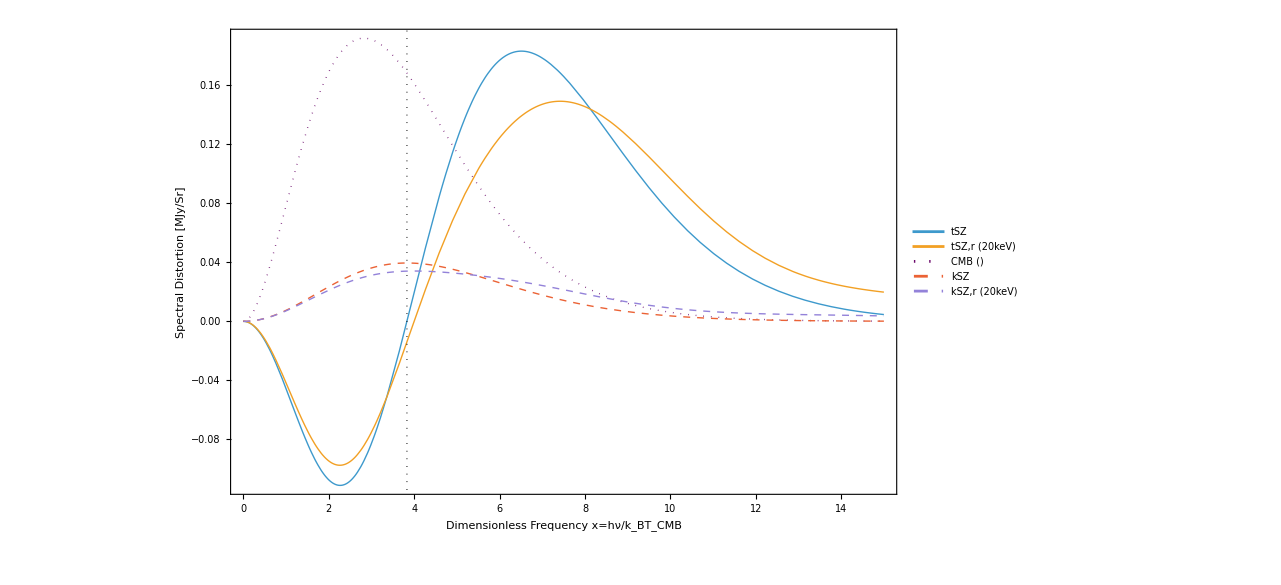

```mathematica
Conv[x_]:=56.71945701*x;
invConv[ν_]:=ν/56.71945701;
topTicks = Table[
{invConv[ν],Style[ν,FontFamily->"Times",FontSize->20]},
{ν,0,1200,200}
];

Plot[{tSZ[270,10^(-4),x],rSZ[270,10^(-4),x,0.0391],PL[270,5*10^(-4),x],kSZ[270,3*10^(-5),x],rkSZ[270,3*10^(-5),x,0.0391]},{x,0,15},
PlotStyle->{{Thick},{Thick},{DarkPurple,Thick, Dotted},{Thick,Dashed},{Thick,Dashed}}, 
Frame->True,
FrameLabel->{
Style["Dimensionless Frequency x=hν/k_BT_CMB"], Style["Spectral Distortion [MJy/Sr]"],Style["Frequency [GHz]"],None},
FrameTicks->{
{Automatic,Automatic},
{Automatic,topTicks}
},
PlotLegends->Placed[LineLegend[{"tSZ","tSZ,r (20keV)","CMB ()", "kSZ", "kSZ,r (20keV)"},LegendLayout->{"Column",2},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.55,0.25}],
Epilog->{{Dotted,Black,AbsoluteThickness[1],Line[{{x0,-0.14},{x0,0.21}}]}},
BaseStyle->{FontFamily->"Times", FontSize->20},
TicksStyle->Directive[FontFamily->"Times", FontSize->20]
]
```

## Kernel Element Generations (courtesy of Jens Chluba)

```mathematica
lmaxv=5; (* set value for kernel setup *)
Kraisef[d_,l_,Klm1f_,Klm2f_]:=-Sqrt[(4l^2-1)/l^2]*(γ*Klm1f[d]-Klm1f[d-1])/p-(l-1)/l*Sqrt[(2l+1)/(2l-3)]*Klm2f[d]
Kswitchf[d_,Klf_]:=Klf[2-d]/.p->-p
K00[d_]:=((γ+p)^(1-d)-(γ-p)^(1-d))/(2 (1-d) p);
K10[d_]:=Kraisef[d,1,K00,K00]
K01[d_]:=Kswitchf[d,K10]

K11[d_]:=Kraisef[d,1,K01,K01]
K21[d_]:=Kraisef[d,2,K11,K01]
K12[d_]:=Kswitchf[d,K21]
K22[d_]:=Kraisef[d,2,K12,K02]
K32[d_]:=Kraisef[d,3,K22,K12]

K20[d_]:=Kraisef[d,2,K10,K00]
K02[d_]:=Kswitchf[d,K20]

K30[d_]:=Kraisef[d,3,K20,K10]
K03[d_]:=Kswitchf[d,K30]

Kmmmd1[m_]:=1/γ^(m+1)Hypergeometric2F1[m/2+1/2,m/2+1,m+3/2,(p/γ)^2] 
Kmmm[m_,d_]:=1/γ^(d+m)Hypergeometric2F1[(d+m)/2,1/2 (1+d+m),3/2+m,p^2/γ^2] 
K20f[d_]:=-(√5 (-(-p+γ)^(1-d)+(p+γ)^(1-d)))/(4 (1-d) p)-1/(2 p)√15 (-1/p √3 γ ((γ (-(-p+γ)^(1-d)+(p+γ)^(1-d)))/(2 (1-d) p)-(-(-p+γ)^(2-d)+(p+γ)^(2-d))/(2 (2-d) p))+1/p √3 ((γ (-(-p+γ)^(2-d)+(p+γ)^(2-d)))/(2 (2-d) p)-(-(-p+γ)^(3-d)+(p+γ)^(3-d))/(2 (3-d) p)));
```

## Recursion Module for Kernel Elements (courtesy of Jens Chluba

```mathematica
Cfunc[l_,m_,s_]:=If[l==0&&m==s==0,1,If[l>=m&&l>=s,Sqrt[(l^2-m^2)*(l^2-s^2)/(4*l^2-1)]/l,0],0];
KllT[m_,lmax_]:=Module[{l,lp,rT=ConstantArray[0,{lmax+1,lmax+1}],GetK,SetK,Kmmmin,Kp1, Ks},

(* make sure the variable d is not set to some value *)
Clear[d];

(* define functions to access right array elements *)
GetK[l_,lp_]:=If[l>=m&&lp>=m,rT[[l+1,lp+1]],0];
SetK[l_,lp_,val_]:=If[l>=m&&lp>=m,rT[[l+1,lp+1]]=val;,rT[[l+1,lp+1]]=0];

(* initial condition K[m,m] *)
Kmmmin=FullSimplify[FunctionExpand[Kmmm[m,d]/.γ->Sqrt[1+p^2],p>0],p>0]/.√(1+p^2)->γ;
SetK[m,m,Kmmmin];

(* K[l,lp] will be generated starting by raising K[m,m] --> K[m+1,m] --> ... *) 
For[lp=m,lp<=lmax,lp++,

For[l=Max[lp,m+1],l<=lmax,l++,

If[l>0,
Kp1=-1/Cfunc[l,m,0]*(γ*GetK[l-1,lp]-(GetK[l-1,lp]/.d->d-1))/p-Cfunc[l-1,m,0]/Cfunc[l,m,0]*GetK[l-2,lp];
SetK[l,lp,Kp1];                                          (* save value *)
];

If[l!=lp,SetK[lp,l,Kp1/.d->2-d/.p->-p]; (* directly set switched kernel value *)];

];
];

Return[rT];
];
```

### Generate Kernel elements

```mathematica
KernelTm = Table[KllT[m,lmaxv],{m,0,lmaxv}];
KernelElementmpos[dv_,pv_,l_,lp_,m_]:=KernelTm[[m+1]][[l+1]][[lp+1]]/.γ->Sqrt[1+p^2]/.d->dv/.p->pv (* m>0 *)

KernelElement[dv_,pv_,l_,lp_,m_]:=If[m>=0,KernelElementmpos[dv,pv,l,lp,m],KernelElementmpos[dv,pv,l,lp,-m]];
```

## Doppler Operator (s=0) Generations

```mathematica
KernelElement[dv_,pv_,l_,lp_,s_,m_]:=If[s==0,KernelElement[dv,pv,l,lp,m],KernelElement2[dv,pv,l,lp,s,m]]
Doppler[dv_,pv_,l_,li_,lp_]:=1/Sqrt[1+pv^2] KernelElement[dv+Oν,-pv,l,li,0,0]*KernelElement[Oν,pv,li,lp,0,0]
Doppler[dv_,pv_,l_,li_,lp_,m_]:=1/Sqrt[1+pv^2] KernelElement[dv+Oν,-pv,l,li,0,m]*KernelElement[Oν,pv,li,lp,0,m]
DopplerAv[dv_,pv_,l_,li_,lp_]:=Sum[Doppler[dv,pv,l,li,l,m],{m,-Min[l,li,lp],Min[l,li,lp]}]
Doppler[dv_,pv_,l_,li_,lp_,si_,sj_,m_]:=1/Sqrt[1+pv^2] KernelElement[dv+Oν,-pv,l,li,si,m]*KernelElement[Oν,pv,li,lp,sj,m]
DopplerAv[dv_,pv_,l_,li_,lp_,si_,sj_]:=Sum[Doppler[dv,pv,l,li,l,si,sj,m],{m,-Min[l,li,lp],Min[l,li,lp]}]
```

## Kinematic Scattering Operators

```mathematica
Scattering[l_]:=DopplerAv[-1,p,l,0,l]/(2l+1)+1/10 DopplerAv[-1,p,l,2,l]/(2l+1)-1; (* Scattering operator in the Cloud rest frame *)

Soperator[l_]:=Sqrt[2l+1]*Sum[Scattering[lp]*Doppler[-1,pβ,l,lp,0,0],{lp,0,3}]; (* Multipole scattering operator in the lab frame *)

FullSoperator:=Sum[Soperator[l]*P[l],{l,0,3}]; (* Full scattering operator in the lab rest frame *)
```

```mathematica
Series[Scattering[3],{p,0,8}]/.OO->Oν//FullSimplify
```

### Expanding p in terms of β

```mathematica
Series[(β/Sqrt[1-β^2]),{β,0,5}]//FullSimplify;
Series[(β/Sqrt[1-β^2])^2,{β,0,5}]//FullSimplify;
```

### Operator expansions

```mathematica
(*Doppler operators*)
Series[Doppler[-1,p,0,0,0,0],{p,0,3}]//FullSimplify
Series[Doppler[-1,p,1,0,0,0],{p,0,3}]//FullSimplify
Series[Doppler[-1,p,2,0,0,0],{p,0,3}]//FullSimplify
Series[Doppler[-1,p,3,0,0,0],{p,0,3}]//FullSimplify

Series[Doppler[-1,p,0,1,0,0],{p,0,3}]//FullSimplify
Series[Doppler[-1,p,1,1,0,0],{p,0,3}]//FullSimplify
Series[Doppler[-1,p,2,1,0,0],{p,0,3}]//FullSimplify
Series[Doppler[-1,p,3,1,0,0],{p,0,3}]//FullSimplify

Series[Doppler[-1,p,0,2,0,0],{p,0,3}]//FullSimplify
Series[Doppler[-1,p,1,2,0,0],{p,0,3}]//FullSimplify
Series[Doppler[-1,p,2,2,0,0],{p,0,3}]//FullSimplify
Series[Doppler[-1,p,3,2,0,0],{p,0,3}]//FullSimplify

Series[Doppler[-1,p,0,3,0,0],{p,0,3}]//FullSimplify
Series[Doppler[-1,p,1,3,0,0],{p,0,3}]//FullSimplify
Series[Doppler[-1,p,2,3,0,0],{p,0,3}]//FullSimplify
Series[Doppler[-1,p,3,3,0,0],{p,0,3}]//FullSimplify
```

```mathematica
(*Scattering operators*)
Series[Scattering[0],{p,0,4}]//FullSimplify
Series[Scattering[1],{p,0,4}]//FullSimplify
Series[Scattering[2],{p,0,4}]//FullSimplify
Series[Scattering[3],{p,0,4}]//FullSimplify
```

#### First order temperature correction

```mathematica
D0=Series[Doppler[-1,p,1,0,0,0],{p,0,1}]//FullSimplify;
D1=Series[Doppler[-1,p,1,1,0,0],{p,0,1}]//FullSimplify;
S0=Series[Scattering[0],{p,0,2}]//FullSimplify;
S1=Series[Scattering[1],{p,0,2}]//FullSimplify;
```

## Doppler Operator Closed Forms

### Closed forms for cosh(arsinh(p))/p^2γ and cosh(arsinh(p))/p^2

```mathematica
(*cosharcsinhbygamma and cosharcsinh include p^-2 factor*)cosharcsinhbygamma[k_, q_,nmax_]:= Sum[1/((2*(n+1))!)*(Product[k^2-(2*m+1)^2,{m,0,n}]-Product[q^2-(2*m+1)^2,{m,0,n}])*p^(2*n),{n,0,nmax}];
cosharcsinh[k_, q_,nmax_]:= Sum[1/((2*(n+1))!)*(Product[k^2-(2*m)^2,{m,0,n}]-Product[q^2-(2*m)^2,{m,0,n}])*p^(2*n),{n,0,nmax}];
```

### K00 K00 Expressions

```mathematica
doublekernelbygamma[a_,b_,nmax_]:=1/(2*(1-a)*(1-b))*Sum[1/((2(n+1))!)*(Product[(2-a-b)^2-(2m+1)^2,{m,0,n}]-Product[(a-b)^2-(2m+1)^2, {m,0,n}])*p^(2*n),{n,0,nmax}];
doublekernel[a_,b_,nmax_]:=1/(2*(1-a)*(1-b))*Sum[1/((2(n+1))!)*(Product[(2-a-b)^2-(2m)^2,{m,0,n}]-Product[(a-b)^2-(2m)^2, {m,0,n}])*p^(2*n),{n,0,nmax}];
```

### Extracting expressions

```mathematica
Dopzerod[nmax_, d_] :=1/(2(1-Oν-d)*(1-Oν))*cosharcsinhbygamma[3-2Oν,d,nmax];
Dopzerodgamma[nmax_, d_] :=1/(2(1-Oν-d)*(1-Oν))*cosharcsinh[3-2Oν,d,nmax];

Dopminoneonezeroone[nmax_]:=(3*(1+p^(-2)))/(2*(-1+Oν)*(-2+Oν))*cosharcsinhbygamma[3-2Oν,-1,nmax]-(3p^(-2))/(2*(3-Oν)*(1-Oν))*cosharcsinh[4-2Oν,-2,nmax]-(3p^(-2))/(2*Oν*(2-Oν))*cosharcsinh[-2,2-2Oν,nmax]+(3p^(-2))/(2*Oν*(3-Oν))*cosharcsinhbygamma[3,3-2Oν,nmax];
```

## Thermal SZ scattering operator

```mathematica
Doppler000[nmax_]:=Sum[(2^(2n+1)p^(2n))/((2(n+1))!)*Product[Oν^2-3Oν-m(m+3),{m,0,n-1}],{n,0,nmax}];
Doppler020[nmax_]:=Sum[(2^(2n+1)p^(2n))/((2(n+1))!)*(5n(n-1))/((n+3)(n+2))*Product[Oν^2-3Oν-m(m+3),{m,0,n-1}],{n,0,nmax}];
tSZ[nmax_,θ_]:=Sum[(θ^n*BesselK[n+2,1/θ])/BesselK[2,1/θ]*(2^n*3((n+3)*n+4))/(2(n+3)!)*Product[OO^2-3OO-m(m+3),{m,0,n-1}],{n,1,nmax}];
```

#### Convergence plot

```mathematica
OOf[k_]:=(-1)^k*Sum[StirlingS2[k,m]*DD[m],{m,1,k}]
ReplOOf[k_]:=Reverse[Table[OO^m->OOf[m],{m,1,2*k}]]
Df[k_]:=x^k*D[1/(Exp[x]-1),{x,k}]
```

```mathematica
plotfunction[θv_,korder_]:=0.0001*270.33*ExpandAll[Normal[Series[Δn[korder,θ],{θ,0,korder}]]]/.ReplOOf[korder+1]/.DD->Df/.θ->θv


f1=plotfunction[θ,1];
f2=plotfunction[θ,2];
f4=plotfunction[θ,4];
f5=plotfunction[θ,5];
f6=plotfunction[θ,6];
f8=plotfunction[θ,8];
f10=plotfunction[θ,10];
f15=plotfunction[θ,15];
f20=plotfunction[θ,20];

fplot1[xv_,θv_]:=f1/θv/.x->xv/.θ->θv;
fplot2[xv_,θv_]:=f2/θv/.x->xv/.θ->θv;
fplot4[xv_,θv_]:=f4/θv/.x->xv/.θ->θv;
fplot5[xv_,θv_]:=f5/θv/.x->xv/.θ->θv;
fplot6[xv_,θv_]:=f6/θv/.x->xv/.θ->θv;
fplot8[xv_,θv_]:=f8/θv/.x->xv/.θ->θv;
fplot10[xv_,θv_]:=f/θv/.x->xv/.θ->θv;
fplot15[xv_,θv_]:=f15/θv/.x->xv/.θ->θv;
fplot20[xv_,θv_]:=f20/θv/.x->xv/.θ->θv;
```

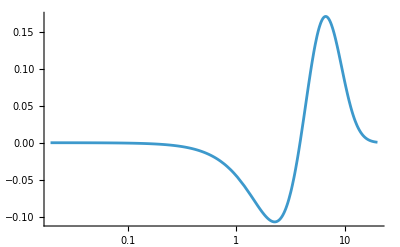

```mathematica
LogLinearPlot[{x^3*fplot10[x,0.01]},{x,0,20},PlotRange->All,WorkingPrecision->30]
```

```mathematica
Conv[x_]:=56.71945701*x;
invConv[ν_]:=ν/56.71945701;
topTicks=Table[{invConv[ν],Style[ν,FontFamily->"Times",FontSize->20]},{ν,0,1200,200}];

Plot[{x^3*fplot1[x,0.0294],x^3*fplot2[x,0.0294],x^3*fplot5[x,0.0294],x^3*fplot10[x,0.0294],x^3*fplot15[x,0.0294]},{x,0,20},PlotStyle->{{Thick}},Frame->True,FrameLabel->{Style["Dimensionless Frequency x=hν/\!\(\*SubscriptBox[\(k\), \(B\)]\)\!\(\*SubscriptBox[\(T\), \(CMB\)]\)"],Style["Spectral Distortion [MJy/Sr]"],Style["Frequency [GHz]"],None},FrameTicks->{{Automatic,Automatic},{Automatic,topTicks}},PlotLegends->Placed[LineLegend[{" order"," order"," order"," order"," order"},LegendLayout->{"Column",1},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.55,0.25}],BaseStyle->{FontFamily->"Times",FontSize->20},TicksStyle->Directive[FontFamily->"Times",FontSize->20],WorkingPrecision->50]
```

## Closed form expressions found by inspection of coefficients

### Expressions for D0l0 and Dl0l

```mathematica
D0l0[l_,nmax_]:=Sum[(-1)^l (2l+1)*(2^(2n+1)p^(2n))/((2(n+1))!)*FactorialPower[n,l]/Pochhammer[n+2,l]*Product[Oν^2-3Oν+2-m(m+1),{m,0,n+1}],{n,0,nmax}];
Dl0l[l_,nmax_]:=1/(Oν^2-3Oν+2-l(l+1))Sum[(-1)^l (2l+1)*(2^(2n+1)p^(2n))/((2(n+1))!)*FactorialPower[n,l]/Pochhammer[n+2,l]*Product[Oν^2-3Oν+2-m(m+1),{m,0,n+1}],{n,0,nmax}];
```

### Expressions for Dlllm where m= +/- l

```mathematica
DOP1111[nmax_]:=Sum[(2^(2n+1)p^(2n))/((2(n+1))!)*(18(n+1))/((n+2)(n+3)(2n+3))*Product[Oν^2-3Oν-4-m(m+5),{m,0,n-1}],{n,0,nmax}];
DOP2222[nmax_]:=Sum[(2^(2n+1)p^(2n))/((2(n+1))!)*(900(n+1)(n+2))/((n+2)(n+3)(n+4)(n+5)(2n+3)(2n+5))*Product[Oν^2-3Oν-10-m(m+7),{m,0,n-1}],{n,0,nmax}];
DOP3333[nmax_]:=Sum[(2^(2n+1)p^(2n))/((2(n+1))!)*(88200(n+1)(n+2)(n+3))/((n+2)(n+3)(n+4)(n+5)(n+6)(n+7)(2n+3)(2n+5)(2n+7))*Product[Oν^2-3Oν-18-m(m+9),{m,0,n-1}],{n,0,nmax}];
DOP4444[nmax_]:=Sum[(2^(2n+1)p^(2n))/((2(n+1))!)*(14288400(n+1)(n+2)(n+3)(n+4))/((n+2)(n+3)(n+4)(n+5)(n+6)(n+7)(n+8)(n+9)(2n+3)(2n+5)(2n+7)(2n+9))*Product[Oν^2-3Oν-28-m(m+11),{m,0,n-1}],{n,0,nmax}];
DOP5555[nmax_]:=Sum[(2^(2n+1)p^(2n))/((2(n+1))!)*((3457792800*(n+1)(n+2)(n+3)(n+4)(n+5))/((n+2)(n+3)(n+4)(n+5)(n+6)(n+7)(n+8)(n+9)(n+10)(n+11)(2n+3)(2n+5)(2n+7)(2n+9)(2n+11)))*Product[Oν^2-3Oν-40-m(m+13),{m,0,n-1}],{n,0,nmax}];
```

### Expression for D121m where m=1

```mathematica
D1211[nmax_]:=Sum[-p^(2n)/5*Product[(2(2+k))/(k(5+k)(5+2k)),{k,1,n-1}]*Product[Oν^2-3Oν-4-m(m+5),{m,0,n-1}],{n,0,nmax}];
```